```mathematica
bvalues={0.1,0.2,0.3,0.4,0.5};
```

```mathematica
dat1=Transpose[{bvalues,{0.3299261628221111,0.4238965675874342,0.5249973004939348,0.376888733388707,0.37034593432617635}}]; (*Near crit E, positive l*)
dat2=Transpose[{bvalues,{0.33981786837282996,0.4223369689702253,0.47136369564211494,0.5076213769565365,0.5341236589903768}}]; (*Near crit E, negative l*)
dat3=Transpose[{bvalues,{0.14192220232073985,0.16922450367918582,0.1899907547771999,0.20938963609365197,0.2354314077381425}}]; (*Far crit E, positive l*)
dat4= Transpose[{bvalues,{0.1434636040881441,0.1746752150103794,0.19893741161751746,0.22090544027032488,0.24017605279149973}}]; (*Far crit E, negative l*)
```

```mathematica
bvalues2=bvalues~Join~{0.6,0.7}
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7}

```mathematica
dat5=Transpose[{bvalues2,{0.3299261628221111,0.4238965675874342,0.5249973004939348,0.376888733388707,0.37034593432617635,0.371634022129736,0.3753555678305307}}]
```

{{0.1,0.329926},{0.2,0.423897},{0.3,0.524997},{0.4,0.376889},{0.5,0.370346},{0.6,0.371634},{0.7,0.375356}}

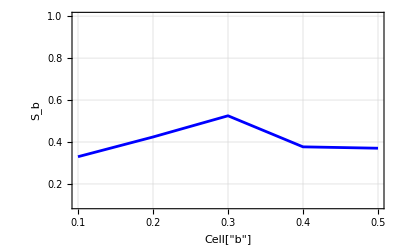

```mathematica
plot1=ListPlot[dat1,
PlotRange->{All,{0.10,1}},
Joined->True,
Frame->True,
Axes->False,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["b",ExpressionUUID->"a5de67bf-52b2-43e1-97cb-18eef1244949"]",Black,Italic,18], Style["S_b",Black,Italic,18]},
RotateLabel->False,
PlotStyle->{Blue,Thickness[0.005]},
GridLines->Automatic,
ImageSize->400]
```

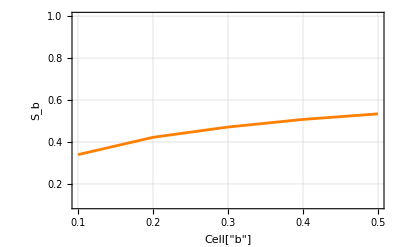

```mathematica
plot2=ListPlot[dat2,
PlotRange->{All,{0.10,1}},
Joined->True,
Frame->True,
Axes->False,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["b",ExpressionUUID->"0491c7b5-7ff5-4cad-84b4-5cb62514828b"]",Black,Italic,18], Style["S_b",Black,Italic,18]},
RotateLabel->False,
PlotStyle->{Orange,Thickness[0.005]},
GridLines->Automatic,
ImageSize->400]
```

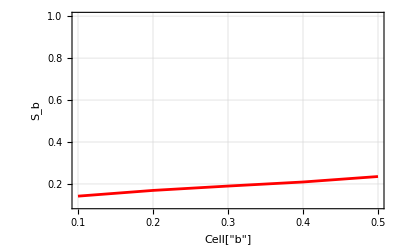

```mathematica
plot3=ListPlot[dat3,
PlotRange->{All,{0.10,1}},
Joined->True,
Frame->True,
Axes->False,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["b",ExpressionUUID->"e96bddfb-3b1a-4334-a9ac-b11abf6eed7b"]",Black,Italic,18], Style["S_b",Black,Italic,18]},
RotateLabel->False,
PlotStyle->{Red,Thickness[0.005]},
GridLines->Automatic,
ImageSize->400]
```

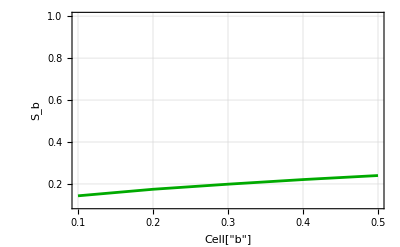

```mathematica
plot4=ListPlot[dat4,
PlotRange->{All,{0.10,1}},
Joined->True,
Frame->True,
Axes->False,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["b",ExpressionUUID->"01835551-834f-477a-8a01-499e38600d20"]",Black,Italic,18], Style["S_b",Black,Italic,18]},
RotateLabel->False,
PlotStyle->{Darker[Green],Thickness[0.005]},
GridLines->Automatic,
ImageSize->400]
```

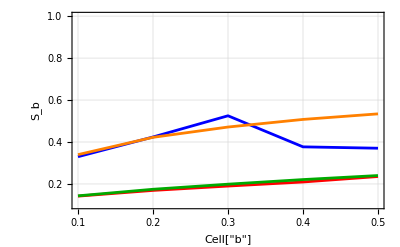

```mathematica
Show[{plot1,plot2,plot3,plot4},
Epilog-> Inset[Framed[Column[{
LineLegend[{Blue}, {"Cell["ℓ>0",ExpressionUUID->"06834660-eff9-4049-92dc-cbd28b9732b1"]: ε=ε̄+0.2"}],
LineLegend[{Orange}, {"Cell["ℓ<0",ExpressionUUID->"5adf8725-8a81-4e89-aca5-3ebea6036b37"]: ε=ε̄+2"}],
LineLegend[{Red}, {"Cell["ℓ>0",ExpressionUUID->"3be8a3bc-f65e-4f20-98e6-ced0a4851127"]: ε=ε̄+0.2"}],
LineLegend[{Darker[Green]}, {"Cell["ℓ<0",ExpressionUUID->"6c2a6853-abdc-483a-935f-0c13d454df13"]: ε=ε̄+2"}]}],RoundingRadius->20,Background->White],{0.17,0.72}]]
```

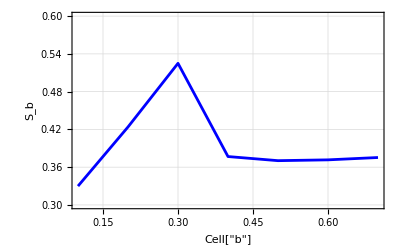

```mathematica
plot5=ListPlot[dat5,
PlotRange->{All,{0.30,0.60}},
Joined->True,
Frame->True,
Axes->False,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["b",ExpressionUUID->"ba81f122-3ddb-4150-8a68-61d114f58777"]",Black,Italic,18], Style["S_b",Black,Italic,18]},
RotateLabel->False,
PlotStyle->{Blue,Thickness[0.005]},
GridLines->Automatic,
ImageSize->400]
```